# Q8

```mathematica
(*a*)
f[x_,y_]:=a*x^2+2h*x*y+b*y^2+2g*x+2f*y+c
(*i*)
h=2;
b=1;
c=-3;
g=-2;
f=-1;
Solve[Det[({{a, h, g}, {h, b, f}, {g, f, c}})]==0,a]
```

SetDelayed::write: Tag Integer in (-1)[x_,y_] is Protected.

$Failed

{{a→4}}

SetDelayed::write: Tag Integer in (-2)[x_,y_] is Protected.

$Failed

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(-2)[x,y]==0,{x,y}]

```mathematica
Clear[f]
(*ii*)
```

-3-4 x+4 x^2-2 y+4 x y+y^2

y==-1-2 x||y==3-2 x

{}

0

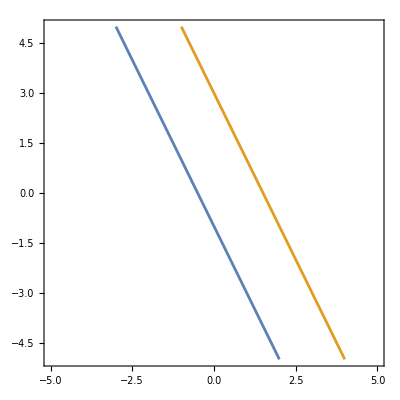

-130+50 x+2 y

-130+2 x+50 y

{{x→5/2,y→5/2}}

25 x^2+2 x y+25 y^2==156

13 x^2+12 y^2==78

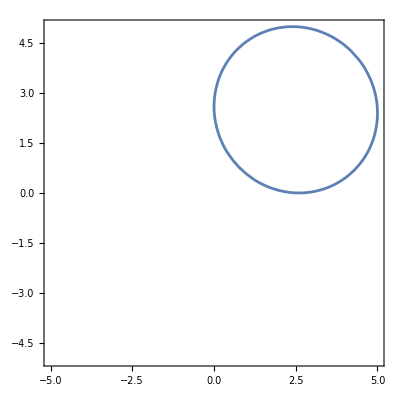

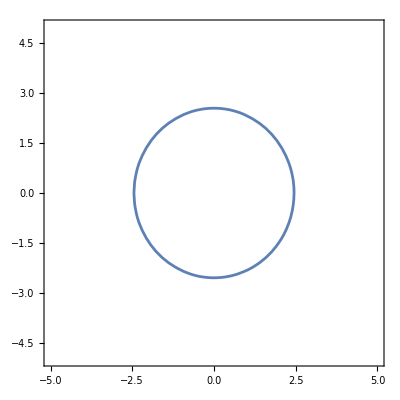

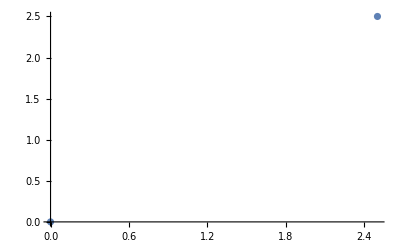

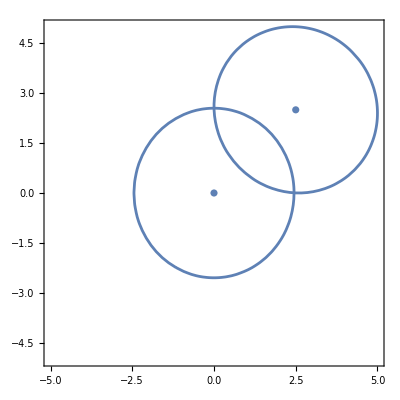

{}

0

```mathematica
f[x_,y_]=4 x^2+4x*y+y^2-4x-2y-3
Reduce[f[x,y]==0,{x,y}]
Solve[{y==-1-2 x,y==3-2 x},{x,y}](*NO solution*)
θ=ArcTan[(-2+2)/(1+4)]
(*iii*)
ContourPlot[{y==-1-2 x,y==3-2 x},{x,-5,5},{y,-5,5}]
(*b*)
Clear[f,g]
g[x_,y_]:=25 x^2+2x*y+25 y^2-130x-130y+169
D[g[x,y],x]
D[g[x,y],y]
Solve[{-130+50 x+2 y==0,-130+2 x+50 y==0},{x,y}]
g[x+5/2,y+5/2]==0//Simplify
f1[x_,y_]:=25 x^2+2 x y+25 y^2-156
t=1/2 ArcTan[Infinity];
f1[x*Cos[Pi/4]-y*Sin[Pi/4],x*Sin[Pi/4]+y*Cos[Pi/4]]==0//Simplify
g1=ContourPlot[g[x,y]==0,{x,-5,5},{y,-5,5}]
g2=ContourPlot[13 x^2+12 y^2-78==0,{x,-5,5},{y,-5,5}]
p=ListPlot[{{2.5,2.5},{0,0}}]
Show[g1,g2,p]
```